```mathematica
Series[Exp[x],{x,0,1}]
```

1+x+O[x]^2

```mathematica
Normal[1+x+O[x]^2]
```

1+x

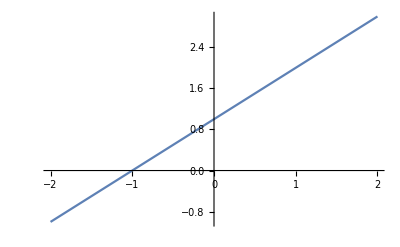

```mathematica
Plot[1+x,{x,-2,2}]
```

```mathematica
Table[Normal[Series[Exp[x],{x,0,i}]], {i, 1, 10}]
```

{1+x,1+x+x^2/2,1+x+x^2/2+x^3/6,1+x+x^2/2+x^3/6+x^4/24,1+x+x^2/2+x^3/6+x^4/24+x^5/120,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800}

```mathematica
Plot[
Table[
Normal[
Series[
Exp[a],
{a,0,i}]],
 {i, 1, 10}],
{x, -5, 5}]
```

-Graphics-

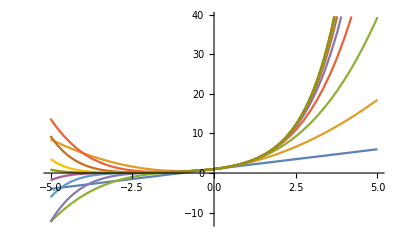

```mathematica
Plot[
{1+x,1+x+x^2/2,1+x+x^2/2+x^3/6,1+x+x^2/2+x^3/6+x^4/24,1+x+x^2/2+x^3/6+x^4/24+x^5/120,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800},
{x, -5, 5}]
```

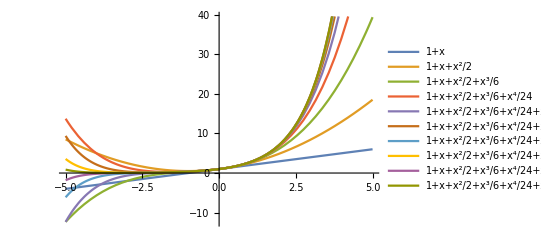

```mathematica
Plot[
{1+x,1+x+x^2/2,1+x+x^2/2+x^3/6,1+x+x^2/2+x^3/6+x^4/24,1+x+x^2/2+x^3/6+x^4/24+x^5/120,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800},
{x, -5, 5}, PlotLegends->"Expressions"]
```

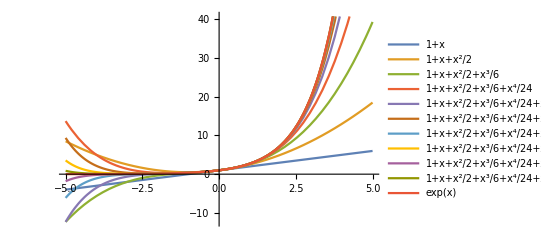

```mathematica
Plot[
{1+x,1+x+x^2/2,1+x+x^2/2+x^3/6,1+x+x^2/2+x^3/6+x^4/24,1+x+x^2/2+x^3/6+x^4/24+x^5/120,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880,1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800,Exp[x]},
{x, -5, 5}, PlotLegends->"Expressions"]
```

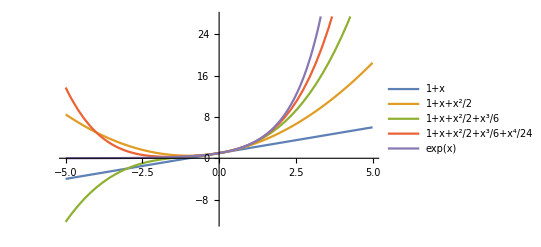

```mathematica
Plot[
{1+x,1+x+x^2/2,1+x+x^2/2+x^3/6,1+x+x^2/2+x^3/6+x^4/24,Exp[x]},
{x, -5, 5}, PlotLegends->"Expressions"]
```

```mathematica
Plot[
{1+x,1+x+x^2/2,1+x+x^2/2+x^3/6,1+x+x^2/2+x^3/6+x^4/24,Exp[x]},
{x, -5, 5}, PlotLegends->"Expressions"]
```

```mathematica
Table[
FullSimplify[
Normalize@{1,Exp[x]}.
Normalize@D[{x,Normal@
Series[Exp[x],{x,0,i}]},x],x∈Reals],
 {i, 1, 10}]
```

{(1+ⅇ^x)/(2 √(ⅇ^x Cosh[x])),(1+ⅇ^x (1+x))/(√((1+ⅇ^(2 x)) (1+(1+x)^2))),(2+ⅇ^x (2+x (2+x)))/(√((1+ⅇ^(2 x)) (8+x (2+x) (4+x (2+x))))),(6+ⅇ^x (6+x (6+x (3+x))))/(√((1+ⅇ^(2 x)) (72+x (6+x (3+x)) (12+x (6+x (3+x)))))),(24+ⅇ^x (24+x (24+x (12+x (4+x)))))/(24 √((1+ⅇ^(2 x)) (1+1/576 (24+x (24+x (12+x (4+x))))^2))),(120+ⅇ^x (120+x (120+x (60+x (20+x (5+x))))))/(120 √((1+ⅇ^(2 x)) (1+(120+x (120+x (60+x (20+x (5+x)))))^2/14400))),(720+ⅇ^x (720+x (720+x (360+x (120+x (30+x (6+x)))))))/(720 √((1+ⅇ^(2 x)) (1+(720+x (720+x (360+x (120+x (30+x (6+x))))))^2/518400))),(5040+ⅇ^x (5040+x (5040+x (2520+x (840+x (210+x (42+x (7+x))))))))/(5040 √((1+ⅇ^(2 x)) (1+(5040+x (5040+x (2520+x (840+x (210+x (42+x (7+x)))))))^2/25401600))),(40320+ⅇ^x (40320+x (40320+x (20160+x (6720+x (1680+x (336+x (56+x (8+x)))))))))/(40320 √((1+ⅇ^(2 x)) (1+(1+x+x^2/2+(x^3 (6720+x (1680+x (336+x (56+x (8+x))))))/40320)^2))),(362880+ⅇ^x (362880+x (362880+x (181440+x (60480+x (15120+x (3024+x (504+x (72+x (9+x))))))))))/(362880 √((1+ⅇ^(2 x)) (1+(1+x+x^2/2+x^3/6+(x^4 (15120+x (3024+x (504+x (72+x (9+x))))))/362880)^2)))}

```mathematica
∈
```

```mathematica
Table[
FullSimplify[
Normalize@{1,Exp[x]}.
Normalize@D[{x,Normal@
Series[Exp[x],{x,0,i}]},x],x∈Reals],
 {i, 1, 5}]
```

{(1+ⅇ^x)/(2 √(ⅇ^x Cosh[x])),(1+ⅇ^x (1+x))/(√((1+ⅇ^(2 x)) (1+(1+x)^2))),(2+ⅇ^x (2+x (2+x)))/(√((1+ⅇ^(2 x)) (8+x (2+x) (4+x (2+x))))),(6+ⅇ^x (6+x (6+x (3+x))))/(√((1+ⅇ^(2 x)) (72+x (6+x (3+x)) (12+x (6+x (3+x)))))),(24+ⅇ^x (24+x (24+x (12+x (4+x)))))/(24 √((1+ⅇ^(2 x)) (1+1/576 (24+x (24+x (12+x (4+x))))^2)))}

```mathematica
Plot[Out[13],{x,-5,5},PlotLegends->"Expressions"]
```

-Graphics-

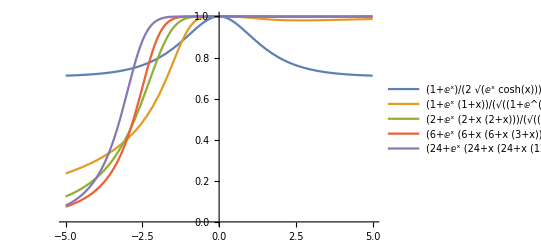

```mathematica
Plot[Out[12],{x,-5,5},PlotLegends->"Expressions"]
```

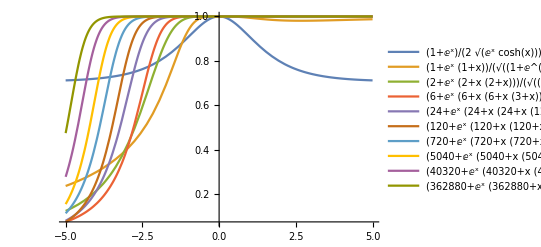

```mathematica
Plot[Out[11],{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
Plot[
Table[
FullSimplify[
Normalize@{1,Exp[x]}.
Normalize@D[{x,Normal@
Series[Exp[x],{x,0,i}]},x],x∈Reals],
 {i, 1, 5}],{x,-5,5},PlotLegends->"Expressions"]
```

General::ivar: -4.9998 is not a valid variable.

General::stop: Further output of General::ivar will be suppressed during this calculation.

-Graphics-

```mathematica
Table[
FullSimplify[
Normalize@{1,Exp[x]}.
Normalize@D[{x,Normal@
Series[Exp[x],{x,0,i}]},x],x∈Reals],
 {i, 1, 50}]
```

$Aborted

```mathematica
Plot[Out[17],{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
FullSimplify[
Table[
Normalize@{1,Exp[x]}.
Normalize@D[{x,Normal@
Series[Exp[x],{x,0,i}]},x],
 {i, 1, 50}],x∈Reals]
```

$Aborted

```mathematica
Table[
Normalize@{1,Exp[x]}.
Normalize@D[{x,Normal@
Series[Exp[x],{x,0,i}]},x],
 {i, 1, 50}]
```

{1/(√2 √(1+ⅇ^(2 Re[x])))+ⅇ^x/(√2 √(1+ⅇ^(2 Re[x]))),48,1/(√(1+ⅇ^(2 Re[x])) √(1+Abs[1+x+46+1+x^49/66000]^2))+(ⅇ^x (1+x+x^2/2+44+1+x^48/125800+x^49/60828186403423610240000000000))/(√(1+ⅇ^(2 Re[x])) √(1+Abs[1+48+1]^2))}
 |  |  |  |

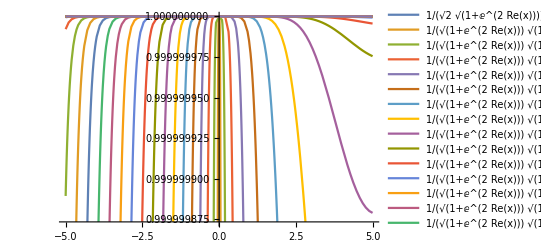

```mathematica
Plot[Out[19],{x,-5,5},PlotLegends->"Expressions"]
```

```mathematica
Integrate[Out[19], {x, -5, 5}]
```

$Aborted

```mathematica
LinguisticAssistant
```

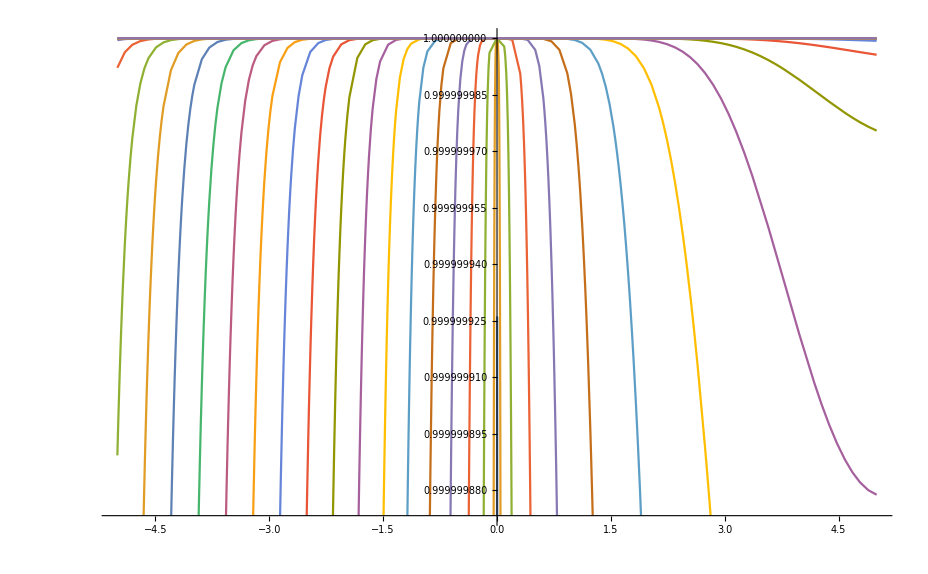

```mathematica
Plot[Out[19],{x,-5,5}]
```

```mathematica
Last@Out@19
```

1/(√(1+ⅇ^(2 Re[x])) √(1+Abs[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800+x^12/479001600+x^13/6227020800+x^14/87178291200+x^15/1307674368000+x^16/20922789888000+x^17/355687428096000+x^18/6402373705728000+x^19/121645100408832000+x^20/2432902008176640000+x^21/51090942171709440000+x^22/1124000727777607680000+x^23/25852016738884976640000+x^24/620448401733239439360000+x^25/15511210043330985984000000+x^26/403291461126605635584000000+x^27/10888869450418352160768000000+x^28/304888344611713860501504000000+x^29/8841761993739701954543616000000+x^30/265252859812191058636308480000000+x^31/8222838654177922817725562880000000+x^32/263130836933693530167218012160000000+x^33/8683317618811886495518194401280000000+x^34/295232799039604140847618609643520000000+x^35/10333147966386144929666651337523200000000+x^36/371993326789901217467999448150835200000000+x^37/13763753091226345046315979581580902400000000+x^38/523022617466601111760007224100074291200000000+x^39/20397882081197443358640281739902897356800000000+x^40/815915283247897734345611269596115894272000000000+x^41/33452526613163807108170062053440751665152000000000+x^42/1405006117752879898543142606244511569936384000000000+x^43/60415263063373835637355132068513997507264512000000000+x^44/2658271574788448768043625811014615890319638528000000000+x^45/119622220865480194561963161495657715064383733760000000000+x^46/5502622159812088949850305428800254892961651752960000000000+x^47/258623241511168180642964355153611979969197632389120000000000+x^48/12413915592536072670862289047373375038521486354677760000000000+x^49/608281864034267560872252163321295376887552831379210240000000000]^2))+(ⅇ^x (1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800+x^12/479001600+x^13/6227020800+x^14/87178291200+x^15/1307674368000+x^16/20922789888000+x^17/355687428096000+x^18/6402373705728000+x^19/121645100408832000+x^20/2432902008176640000+x^21/51090942171709440000+x^22/1124000727777607680000+x^23/25852016738884976640000+x^24/620448401733239439360000+x^25/15511210043330985984000000+x^26/403291461126605635584000000+x^27/10888869450418352160768000000+x^28/304888344611713860501504000000+x^29/8841761993739701954543616000000+x^30/265252859812191058636308480000000+x^31/8222838654177922817725562880000000+x^32/263130836933693530167218012160000000+x^33/8683317618811886495518194401280000000+x^34/295232799039604140847618609643520000000+x^35/10333147966386144929666651337523200000000+x^36/371993326789901217467999448150835200000000+x^37/13763753091226345046315979581580902400000000+x^38/523022617466601111760007224100074291200000000+x^39/20397882081197443358640281739902897356800000000+x^40/815915283247897734345611269596115894272000000000+x^41/33452526613163807108170062053440751665152000000000+x^42/1405006117752879898543142606244511569936384000000000+x^43/60415263063373835637355132068513997507264512000000000+x^44/2658271574788448768043625811014615890319638528000000000+x^45/119622220865480194561963161495657715064383733760000000000+x^46/5502622159812088949850305428800254892961651752960000000000+x^47/258623241511168180642964355153611979969197632389120000000000+x^48/12413915592536072670862289047373375038521486354677760000000000+x^49/608281864034267560872252163321295376887552831379210240000000000))/(√(1+ⅇ^(2 Re[x])) √(1+Abs[1+x+x^2/2+x^3/6+x^4/24+x^5/120+x^6/720+x^7/5040+x^8/40320+x^9/362880+x^10/3628800+x^11/39916800+x^12/479001600+x^13/6227020800+x^14/87178291200+x^15/1307674368000+x^16/20922789888000+x^17/355687428096000+x^18/6402373705728000+x^19/121645100408832000+x^20/2432902008176640000+x^21/51090942171709440000+x^22/1124000727777607680000+x^23/25852016738884976640000+x^24/620448401733239439360000+x^25/15511210043330985984000000+x^26/403291461126605635584000000+x^27/10888869450418352160768000000+x^28/304888344611713860501504000000+x^29/8841761993739701954543616000000+x^30/265252859812191058636308480000000+x^31/8222838654177922817725562880000000+x^32/263130836933693530167218012160000000+x^33/8683317618811886495518194401280000000+x^34/295232799039604140847618609643520000000+x^35/10333147966386144929666651337523200000000+x^36/371993326789901217467999448150835200000000+x^37/13763753091226345046315979581580902400000000+x^38/523022617466601111760007224100074291200000000+x^39/20397882081197443358640281739902897356800000000+x^40/815915283247897734345611269596115894272000000000+x^41/33452526613163807108170062053440751665152000000000+x^42/1405006117752879898543142606244511569936384000000000+x^43/60415263063373835637355132068513997507264512000000000+x^44/2658271574788448768043625811014615890319638528000000000+x^45/119622220865480194561963161495657715064383733760000000000+x^46/5502622159812088949850305428800254892961651752960000000000+x^47/258623241511168180642964355153611979969197632389120000000000+x^48/12413915592536072670862289047373375038521486354677760000000000+x^49/608281864034267560872252163321295376887552831379210240000000000]^2))

```mathematica
FullSimplify[
Last@Out@19, x∈Reals]
```

$Aborted

```mathematica
FullForm@Last@Out@19
```

Plus[Times[Power[Plus[1,Power[E,Times[2,Re[x]]]],Rational[-1,2]],Power[Plus[1,Power[Abs[Plus[1,x,Times[Rational[1,2],Power[x,2]],Times[Rational[1,6],Power[x,3]],Times[Rational[1,24],Power[x,4]],Times[Rational[1,120],Power[x,5]],Times[Rational[1,720],Power[x,6]],Times[Rational[1,5040],Power[x,7]],Times[Rational[1,40320],Power[x,8]],Times[Rational[1,362880],Power[x,9]],Times[Rational[1,3628800],Power[x,10]],Times[Rational[1,39916800],Power[x,11]],Times[Rational[1,479001600],Power[x,12]],Times[Rational[1,6227020800],Power[x,13]],Times[Rational[1,87178291200],Power[x,14]],Times[Rational[1,1307674368000],Power[x,15]],Times[Rational[1,20922789888000],Power[x,16]],Times[Rational[1,355687428096000],Power[x,17]],Times[Rational[1,6402373705728000],Power[x,18]],Times[Rational[1,121645100408832000],Power[x,19]],Times[Rational[1,2432902008176640000],Power[x,20]],Times[Rational[1,51090942171709440000],Power[x,21]],Times[Rational[1,1124000727777607680000],Power[x,22]],Times[Rational[1,25852016738884976640000],Power[x,23]],Times[Rational[1,620448401733239439360000],Power[x,24]],Times[Rational[1,15511210043330985984000000],Power[x,25]],Times[Rational[1,403291461126605635584000000],Power[x,26]],Times[Rational[1,10888869450418352160768000000],Power[x,27]],Times[Rational[1,304888344611713860501504000000],Power[x,28]],Times[Rational[1,8841761993739701954543616000000],Power[x,29]],Times[Rational[1,265252859812191058636308480000000],Power[x,30]],Times[Rational[1,8222838654177922817725562880000000],Power[x,31]],Times[Rational[1,263130836933693530167218012160000000],Power[x,32]],Times[Rational[1,8683317618811886495518194401280000000],Power[x,33]],Times[Rational[1,295232799039604140847618609643520000000],Power[x,34]],Times[Rational[1,10333147966386144929666651337523200000000],Power[x,35]],Times[Rational[1,371993326789901217467999448150835200000000],Power[x,36]],Times[Rational[1,13763753091226345046315979581580902400000000],Power[x,37]],Times[Rational[1,523022617466601111760007224100074291200000000],Power[x,38]],Times[Rational[1,20397882081197443358640281739902897356800000000],Power[x,39]],Times[Rational[1,815915283247897734345611269596115894272000000000],Power[x,40]],Times[Rational[1,33452526613163807108170062053440751665152000000000],Power[x,41]],Times[Rational[1,1405006117752879898543142606244511569936384000000000],Power[x,42]],Times[Rational[1,60415263063373835637355132068513997507264512000000000],Power[x,43]],Times[Rational[1,2658271574788448768043625811014615890319638528000000000],Power[x,44]],Times[Rational[1,119622220865480194561963161495657715064383733760000000000],Power[x,45]],Times[Rational[1,5502622159812088949850305428800254892961651752960000000000],Power[x,46]],Times[Rational[1,258623241511168180642964355153611979969197632389120000000000],Power[x,47]],Times[Rational[1,12413915592536072670862289047373375038521486354677760000000000],Power[x,48]],Times[Rational[1,608281864034267560872252163321295376887552831379210240000000000],Power[x,49]]]],2]],Rational[-1,2]]],Times[Power[E,x],Power[Plus[1,Power[E,Times[2,Re[x]]]],Rational[-1,2]],Plus[1,x,Times[Rational[1,2],Power[x,2]],Times[Rational[1,6],Power[x,3]],Times[Rational[1,24],Power[x,4]],Times[Rational[1,120],Power[x,5]],Times[Rational[1,720],Power[x,6]],Times[Rational[1,5040],Power[x,7]],Times[Rational[1,40320],Power[x,8]],Times[Rational[1,362880],Power[x,9]],Times[Rational[1,3628800],Power[x,10]],Times[Rational[1,39916800],Power[x,11]],Times[Rational[1,479001600],Power[x,12]],Times[Rational[1,6227020800],Power[x,13]],Times[Rational[1,87178291200],Power[x,14]],Times[Rational[1,1307674368000],Power[x,15]],Times[Rational[1,20922789888000],Power[x,16]],Times[Rational[1,355687428096000],Power[x,17]],Times[Rational[1,6402373705728000],Power[x,18]],Times[Rational[1,121645100408832000],Power[x,19]],Times[Rational[1,2432902008176640000],Power[x,20]],Times[Rational[1,51090942171709440000],Power[x,21]],Times[Rational[1,1124000727777607680000],Power[x,22]],Times[Rational[1,25852016738884976640000],Power[x,23]],Times[Rational[1,620448401733239439360000],Power[x,24]],Times[Rational[1,15511210043330985984000000],Power[x,25]],Times[Rational[1,403291461126605635584000000],Power[x,26]],Times[Rational[1,10888869450418352160768000000],Power[x,27]],Times[Rational[1,304888344611713860501504000000],Power[x,28]],Times[Rational[1,8841761993739701954543616000000],Power[x,29]],Times[Rational[1,265252859812191058636308480000000],Power[x,30]],Times[Rational[1,8222838654177922817725562880000000],Power[x,31]],Times[Rational[1,263130836933693530167218012160000000],Power[x,32]],Times[Rational[1,8683317618811886495518194401280000000],Power[x,33]],Times[Rational[1,295232799039604140847618609643520000000],Power[x,34]],Times[Rational[1,10333147966386144929666651337523200000000],Power[x,35]],Times[Rational[1,371993326789901217467999448150835200000000],Power[x,36]],Times[Rational[1,13763753091226345046315979581580902400000000],Power[x,37]],Times[Rational[1,523022617466601111760007224100074291200000000],Power[x,38]],Times[Rational[1,20397882081197443358640281739902897356800000000],Power[x,39]],Times[Rational[1,815915283247897734345611269596115894272000000000],Power[x,40]],Times[Rational[1,33452526613163807108170062053440751665152000000000],Power[x,41]],Times[Rational[1,1405006117752879898543142606244511569936384000000000],Power[x,42]],Times[Rational[1,60415263063373835637355132068513997507264512000000000],Power[x,43]],Times[Rational[1,2658271574788448768043625811014615890319638528000000000],Power[x,44]],Times[Rational[1,119622220865480194561963161495657715064383733760000000000],Power[x,45]],Times[Rational[1,5502622159812088949850305428800254892961651752960000000000],Power[x,46]],Times[Rational[1,258623241511168180642964355153611979969197632389120000000000],Power[x,47]],Times[Rational[1,12413915592536072670862289047373375038521486354677760000000000],Power[x,48]],Times[Rational[1,608281864034267560872252163321295376887552831379210240000000000],Power[x,49]]],Power[Plus[1,Power[Abs[Plus[1,x,Times[Rational[1,2],Power[x,2]],Times[Rational[1,6],Power[x,3]],Times[Rational[1,24],Power[x,4]],Times[Rational[1,120],Power[x,5]],Times[Rational[1,720],Power[x,6]],Times[Rational[1,5040],Power[x,7]],Times[Rational[1,40320],Power[x,8]],Times[Rational[1,362880],Power[x,9]],Times[Rational[1,3628800],Power[x,10]],Times[Rational[1,39916800],Power[x,11]],Times[Rational[1,479001600],Power[x,12]],Times[Rational[1,6227020800],Power[x,13]],Times[Rational[1,87178291200],Power[x,14]],Times[Rational[1,1307674368000],Power[x,15]],Times[Rational[1,20922789888000],Power[x,16]],Times[Rational[1,355687428096000],Power[x,17]],Times[Rational[1,6402373705728000],Power[x,18]],Times[Rational[1,121645100408832000],Power[x,19]],Times[Rational[1,2432902008176640000],Power[x,20]],Times[Rational[1,51090942171709440000],Power[x,21]],Times[Rational[1,1124000727777607680000],Power[x,22]],Times[Rational[1,25852016738884976640000],Power[x,23]],Times[Rational[1,620448401733239439360000],Power[x,24]],Times[Rational[1,15511210043330985984000000],Power[x,25]],Times[Rational[1,403291461126605635584000000],Power[x,26]],Times[Rational[1,10888869450418352160768000000],Power[x,27]],Times[Rational[1,304888344611713860501504000000],Power[x,28]],Times[Rational[1,8841761993739701954543616000000],Power[x,29]],Times[Rational[1,265252859812191058636308480000000],Power[x,30]],Times[Rational[1,8222838654177922817725562880000000],Power[x,31]],Times[Rational[1,263130836933693530167218012160000000],Power[x,32]],Times[Rational[1,8683317618811886495518194401280000000],Power[x,33]],Times[Rational[1,295232799039604140847618609643520000000],Power[x,34]],Times[Rational[1,10333147966386144929666651337523200000000],Power[x,35]],Times[Rational[1,371993326789901217467999448150835200000000],Power[x,36]],Times[Rational[1,13763753091226345046315979581580902400000000],Power[x,37]],Times[Rational[1,523022617466601111760007224100074291200000000],Power[x,38]],Times[Rational[1,20397882081197443358640281739902897356800000000],Power[x,39]],Times[Rational[1,815915283247897734345611269596115894272000000000],Power[x,40]],Times[Rational[1,33452526613163807108170062053440751665152000000000],Power[x,41]],Times[Rational[1,1405006117752879898543142606244511569936384000000000],Power[x,42]],Times[Rational[1,60415263063373835637355132068513997507264512000000000],Power[x,43]],Times[Rational[1,2658271574788448768043625811014615890319638528000000000],Power[x,44]],Times[Rational[1,119622220865480194561963161495657715064383733760000000000],Power[x,45]],Times[Rational[1,5502622159812088949850305428800254892961651752960000000000],Power[x,46]],Times[Rational[1,258623241511168180642964355153611979969197632389120000000000],Power[x,47]],Times[Rational[1,12413915592536072670862289047373375038521486354677760000000000],Power[x,48]],Times[Rational[1,608281864034267560872252163321295376887552831379210240000000000],Power[x,49]]]],2]],Rational[-1,2]]]]

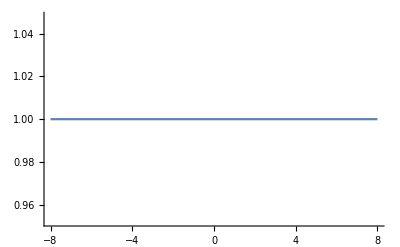

```mathematica
Plot[%26,{x,-8,8}]
```

```mathematica
CountryData["UnitedStates", "Religions"]
```

{Entity[Religion,Protestant],Roman Catholic Church,Entity[Religion,LatterDaySaints],Islam,Judaism,Buddhism,Entity[Religion,OtherNone]}

```mathematica
CountryData["UnitedStates", "ReligionsFractions"]
```

{Entity[Religion,Protestant]→0.513,Roman Catholic Church→0.239,Entity[Religion,LatterDaySaints]→0.017,Judaism→0.017,Entity[Religion,OtherChristian]→0.016,Buddhism→0.007,Islam→0.006,Entity[Religion,OtherNone]→0.186}

```mathematica
Map[PercentForm@Last@#&,
{Entity["Religion","Protestant"]->0.513,Entity["Religion","RomanCatholic"]->0.239,Entity["Religion","LatterDaySaints"]->0.017,Entity["Religion","Jewish"]->0.017,Entity["Religion","OtherChristian"]->0.016,Entity["Religion","Buddhist"]->0.007,Entity["Religion","Muslim"]->0.006,Entity["Religion","OtherNone"]->0.186}]
```

{51.3%,23.9%,1.7%,1.7%,1.6%,0.7%,0.6%,18.6%}

```mathematica
Join@
Map[CountryData[#, "Religions"]&, CountryData[]]
```

{{Entity[Religion,SunniMuslim],Entity[Religion,ShiaMuslim],Entity[Religion,OtherNone]},Missing[NotAvailable],{Islam,Entity[Religion,AlbanianOrthodox],Roman Catholic Church},{Entity[Religion,SunniMuslim],Entity[Religion,ChristianJewish]},{Congregational Christian Church,Roman Catholic Church,Entity[Religion,OtherNone]},{Roman Catholic Church},{Entity[Religion,Indigenous],Roman Catholic Church,Entity[Religion,Protestant]},{Entity[Religion,Protestant],Anglican Communion,Methodism,Roman Catholic Church,Christianity,Entity[Religion,OtherNone]},{Anglican Communion,Entity[Religion,SeventhDayAdventist],Pentecostalism,Entity[Religion,Moravian],Roman Catholic Church,Methodism,Entity[Religion,OtherChristian],Baptist Church,Entity[Religion,ChurchOfGod],Entity[Religion,OtherNone]},{Roman Catholic Church,Judaism,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Entity[Religion,ArmenianApostolic],Christianity,Entity[Religion,Yezidi]},{Roman Catholic Church,Entity[Religion,Protestant],Hinduism,Islam,Confucianism,Judaism,Entity[Religion,OtherNone]},{Roman Catholic Church,Anglican Communion,Entity[Religion,Protestant],Buddhism,Islam,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Islam,Entity[Religion,OtherNone]},{Islam,Russian Orthodox Church,Entity[Religion,ArmenianOrthodox],Entity[Religion,OtherNone]},{Baptist Church,Christianity,Anglican Communion,Roman Catholic Church,Pentecostalism,Entity[Religion,ChurchOfGod],Methodism,Entity[Religion,OtherNone]},{Islam,Christianity,Entity[Religion,OtherNone]},{Islam,Hinduism,Entity[Religion,OtherNone]},{Anglican Communion,Pentecostalism,Entity[Religion,Protestant],Entity[Religion,OtherChristian],Methodism,Roman Catholic Church,Entity[Religion,OtherNone]},{Entity[Religion,EasternOrthodox],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Anglican Communion,Entity[Religion,SeventhDayAdventist],Mennonite Church,Methodism,Entity[Religion,JehovahsWitness],Entity[Religion,OtherNone]},{Roman Catholic Church,Islam,Entity[Religion,Vodoun],Entity[Religion,OtherChristian],Entity[Religion,Celestial],Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Anglican Communion,Entity[Religion,Protestant],Roman Catholic Church,Entity[Religion,AfricanMethodistEpiscopal],Entity[Religion,OtherNone]},{Entity[Religion,LamaisticBuddhist],Hinduism},{Roman Catholic Church,Entity[Religion,Protestant]},Missing[NotAvailable],{Islam,Entity[Religion,OrthodoxChristian],Roman Catholic Church,Entity[Religion,OtherNone]},{Christianity,Entity[Religion,Badimo],Entity[Religion,OtherNone]},Missing[NotAvailable],{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,Spiritualist],Entity[Religion,BantuVoodoo],Entity[Religion,OtherNone]},Missing[NotAvailable],{Methodism,Anglican Communion,Entity[Religion,Protestant],Roman Catholic Church,Entity[Religion,ChurchOfGod],Entity[Religion,SeventhDayAdventist],Baptist Church,Entity[Religion,JehovahsWitness],Entity[Religion,OtherNone]},{Islam,Buddhism,Christianity,Entity[Religion,Indigenous]},{Entity[Religion,BulgarianOrthodox],Islam,Christianity,Entity[Religion,OtherNone]},{Islam,Entity[Religion,Indigenous],Christianity},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,Indigenous],Islam},{Entity[Religion,TheravadaBuddhist],Entity[Religion,OtherNone]},{Entity[Religion,Indigenous],Christianity,Islam},{Roman Catholic Church,Entity[Religion,ProtestantUnitedChurch],Anglican Communion,Christianity,Baptist Church,Lutheran Church,Islam,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant]},{Entity[Religion,ChurchOfGod],Entity[Religion,UnitedChurch],Roman Catholic Church,Baptist Church,Entity[Religion,SeventhDayAdventist],Anglican Communion,Pentecostalism,Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Entity[Religion,Indigenous],Entity[Religion,Protestant],Roman Catholic Church,Islam},{Islam,Entity[Religion,Catholic],Entity[Religion,Protestant],Entity[Religion,Animist],Entity[Religion,Atheist],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Evangelical],Entity[Religion,JehovahsWitness],Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Entity[Religion,Daoist],Buddhism,Christianity,Islam},{Buddhism,Islam,Christianity,Entity[Religion,OtherNone]},{Entity[Religion,SunniMuslim],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OtherNone]},{Entity[Religion,SunniMuslim],Roman Catholic Church},{Entity[Religion,CookIslandsChristianChurch],Roman Catholic Church,Entity[Religion,SeventhDayAdventist],Entity[Religion,Protestant],Entity[Religion,LatterDaySaints],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Evangelical],Entity[Religion,JehovahsWitness],Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OrthodoxChristian],Islam,Christianity,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,JehovahsWitness],Judaism,Entity[Religion,Santeria]},Missing[NotAvailable],{Greek Orthodox Christian Church,Islam,Entity[Religion,MaroniteCatholic],Entity[Religion,ArmenianApostolic],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,Kimbanguist],Islam,Entity[Religion,Indigenous],Entity[Religion,Syncretic]},{Entity[Religion,EvangelicalLutheran],Entity[Religion,OtherChristian],Islam},{Islam,Christianity},{Roman Catholic Church,Entity[Religion,OtherChristian],Entity[Religion,SeventhDayAdventist],Pentecostalism,Baptist Church,Methodism,Entity[Religion,Rastafarian],Entity[Religion,ChurchOfGod],Entity[Religion,JehovahsWitness],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OtherNone]},{Roman Catholic Church,Islam,Entity[Religion,Protestant]},{Roman Catholic Church,Entity[Religion,OtherNone]},{Islam,Entity[Religion,Coptic],Christianity},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,JehovahsWitness],Entity[Religion,Mormon],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Indigenous]},{Islam,Entity[Religion,Coptic],Roman Catholic Church,Entity[Religion,Protestant]},{Entity[Religion,EvangelicalLutheran],Entity[Religion,OrthodoxChristian],Christianity,Entity[Religion,OtherNone]},{Ethiopian Orthodox Christian Church,Islam,Entity[Religion,Protestant],Entity[Religion,Animist],Entity[Religion,OtherNone]},{Christianity,Entity[Religion,OtherNone]},{Entity[Religion,EvangelicalLutheran],Entity[Religion,OtherNone]},{Methodism,Hinduism,Roman Catholic Church,Islam,Entity[Religion,OtherChristian],Entity[Religion,AssemblyOfGod],Entity[Religion,SeventhDayAdventist],Entity[Religion,OtherNone]},{Entity[Religion,LutheranNationalChurch],Entity[Religion,Orthodox],Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Roman Catholic Church,Islam,Entity[Religion,Protestant],Judaism,Entity[Religion,OtherNone]},{Roman Catholic Church},{Entity[Religion,Protestant],Roman Catholic Church,Entity[Religion,OtherNone]},Missing[NotAvailable],{Christianity,Entity[Religion,Animist],Islam},{Islam,Christianity,Entity[Religion,Indigenous]},{Islam,Christianity},{Entity[Religion,OrthodoxChristian],Islam,Entity[Religion,ArmenianGregorian],Roman Catholic Church,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Islam,Entity[Religion,OtherNone]},{Entity[Religion,PentecostalCharismatic],Entity[Religion,Protestant],Islam,Roman Catholic Church,Entity[Religion,OtherChristian],Entity[Religion,Indigenous],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,ChurchOfEngland],Islam,Christianity,Judaism,Hinduism,Entity[Religion,OtherNone]},{Greek Orthodox Christian Church,Islam,Entity[Religion,OtherNone]},{Entity[Religion,EvangelicalLutheran]},{Roman Catholic Church,Anglican Communion,Entity[Religion,Protestant]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,Indigenous]},{Anglican Communion,Roman Catholic Church,Presbyterian Church,Baptist Church,Congregational Christian Church,Methodism},{Islam,Christianity,Entity[Religion,Indigenous]},{Islam,Entity[Religion,Indigenous],Christianity},{Hinduism,Entity[Religion,OtherChristian],Pentecostalism,Roman Catholic Church,Islam,Anglican Communion,Entity[Religion,SeventhDayAdventist],Methodism,Entity[Religion,JehovahsWitness],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Pentecostalism,Seventh-day Adventist Church,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant]},{Entity[Religion,Indigenous],Christianity},{Roman Catholic Church,Entity[Religion,Calvinist],Lutheran Church,Entity[Religion,GreekCatholic],Christianity,Entity[Religion,OtherNone]},{Entity[Religion,LutheranChurchOfIceland],Entity[Religion,OtherChristian],Roman Catholic Church,Entity[Religion,ReykjavikFreeChurch],Entity[Religion,HafnarfjorourFreeChurch],Entity[Religion,OtherNone]},{Hinduism,Islam,Christianity,Sikhism,Entity[Religion,OtherNone]},{Islam,Entity[Religion,Protestant],Roman Catholic Church,Hinduism,Entity[Religion,OtherNone]},{Entity[Religion,ShiaMuslim],Entity[Religion,SunniMuslim],Zoroastrianism,Judaism,Christianity,Bahá'í Faith},{Islam,Entity[Religion,SunniMuslim],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,ChurchOfIreland],Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Anglican Communion,Roman Catholic Church,Methodism,Baptist Church,Presbyterian Church,Entity[Religion,SocietyOfFriends]},{Judaism,Islam,Entity[Religion,ArabChristian],Druze,Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Judaism,Islam},{Islam,Christianity,Entity[Religion,Indigenous],Entity[Religion,OtherNone]},{Entity[Religion,ChurchOfGod],Entity[Religion,SeventhDayAdventist],Pentecostalism,Entity[Religion,OtherChristian],Baptist Church,Anglican Communion,Roman Catholic Church,Entity[Religion,OtherNone]},{Entity[Religion,ShintoBuddhist],Christianity,Entity[Religion,OtherNone]},{Anglican Communion,Roman Catholic Church,Baptist Church,Congregational Christian Church,Methodism,Presbyterian Church},{Entity[Religion,SunniMuslim],Christianity,Entity[Religion,OtherNone]},{Islam,Russian Orthodox Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Entity[Religion,Protestant],Roman Catholic Church,Islam,Entity[Religion,Indigenous],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,SeventhDayAdventist],Islam,Bahá'í Faith,Entity[Religion,LatterDaySaints],Entity[Religion,ChurchOfGod]},{Islam,Roman Catholic Church,Entity[Religion,SerbianOrthodox]},{Entity[Religion,SunniMuslim],Entity[Religion,ShiaMuslim],Christianity,Hinduism,Entity[Religion,Parsi]},{Islam,Russian Orthodox Church,Entity[Religion,OtherNone]},{Buddhism,Christianity,Entity[Religion,OtherNone]},{Lutheran Church,Entity[Religion,Orthodox],Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Islam,Entity[Religion,ShiaMuslim],Entity[Religion,SunniMuslim],Druze,Entity[Religion,Ismailite],Entity[Religion,Alawite],Entity[Religion,Nusayri],Christianity,Entity[Religion,MaroniteCatholic],Greek Orthodox Christian Church,Entity[Religion,MelkiteCatholic],Entity[Religion,ArmenianOrthodox],Entity[Religion,SyrianCatholic],Entity[Religion,ArmenianCatholic],Entity[Religion,SyrianOrthodox],Roman Catholic Church,Entity[Religion,Chaldean],Entity[Religion,Assyrian],Entity[Religion,Coptic],Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Christianity,Entity[Religion,Indigenous]},{Entity[Religion,Indigenous],Christianity,Islam},{Entity[Religion,SunniMuslim],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Roman Catholic Church,Russian Orthodox Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Judaism,Islam},{Buddhism,Roman Catholic Church,Entity[Religion,OtherNone]},{Entity[Religion,MacedonianOrthodox],Islam,Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Entity[Religion,Indigenous],Christianity,Islam},{Christianity,Islam,Entity[Religion,OtherNone]},{Islam,Buddhism,Christianity,Hinduism,Taoism,Confucianism,Entity[Religion,OtherNone]},{Entity[Religion,SunniMuslim]},{Islam,Entity[Religion,Indigenous],Christianity},{Roman Catholic Church},{Entity[Religion,Protestant],Entity[Religion,AssemblyOfGod],Roman Catholic Church,Christianity,Entity[Religion,BukotNanJesus],Entity[Religion,LatterDaySaints],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Hinduism,Islam,Entity[Religion,OtherNone]},{Islam},{Hinduism,Roman Catholic Church,Islam,Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Islam,Christianity},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Entity[Religion,EasternOrthodox],Judaism,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OtherNone]},{Entity[Religion,BuddhistLamaist],Islam,Entity[Religion,Shamanism],Christianity,Entity[Religion,OtherNone]},{Entity[Religion,Orthodox],Islam,Roman Catholic Church,Entity[Religion,OtherNone]},{Anglican Communion,Methodism,Roman Catholic Church,Pentecostalism,Entity[Religion,SeventhDayAdventist],Christianity},{Islam,Christianity,Judaism},{Roman Catholic Church,Islam,Entity[Religion,ZionistChristian],Entity[Religion,OtherNone]},{Buddhism,Islam,Christianity,Entity[Religion,Animist],Roman Catholic Church,Entity[Religion,OtherNone]},{Lutheran Church,Christianity,Entity[Religion,Indigenous]},{Entity[Religion,Protestant],Roman Catholic Church},{Hinduism,Buddhism,Islam,Entity[Religion,Kirant],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,DutchReformed],Entity[Religion,Calvinist],Islam,Entity[Religion,Protestant],Entity[Religion,Other],Entity[Religion,None]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Anglican Communion,Roman Catholic Church,Presbyterian Church,Christianity,Methodism,Pentecostalism,Baptist Church,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Evangelical],Entity[Religion,Moravian],Entity[Religion,Episcopalian],Entity[Religion,OtherNone]},{Islam,Entity[Religion,Indigenous],Christianity},{Islam,Christianity,Entity[Religion,Indigenous]},{Entity[Religion,EkalesiaNiue],Entity[Religion,LatterDaySaints],Roman Catholic Church,Entity[Religion,JehovahsWitness],Entity[Religion,SeventhDayAdventist],Entity[Religion,OtherNone]},{Anglican Communion,Roman Catholic Church,Entity[Religion,UnitingChurchInAustralia],Entity[Religion,OtherChristian],Entity[Religion,SeventhDayAdventist],Entity[Religion,OtherNone]},{Christianity},{Entity[Religion,BuddhistConfucian],Christianity,Entity[Religion,Chondogyo]},{Entity[Religion,ChurchOfNorway],Christianity,Islam,Roman Catholic Church,Pentecostalism,Entity[Religion,OtherNone]},{Entity[Religion,IbadhiMuslim],Entity[Religion,SunniMuslim],Entity[Religion,ShiaMuslim],Hinduism},{Entity[Religion,SunniMuslim],Entity[Religion,ShiaMuslim],Christianity,Hinduism},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,Modekngei],Entity[Religion,SeventhDayAdventist],Entity[Religion,JehovahsWitness],Entity[Religion,LatterDaySaints],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant]},{Roman Catholic Church,Entity[Religion,EvangelicalLutheran],Entity[Religion,UnitedChurch],Entity[Religion,SeventhDayAdventist],Entity[Religion,Protestant],Pentecostalism,Entity[Religion,EvangelicalAlliance],Anglican Communion,Baptist Church,Bahá'í Faith,Entity[Religion,Indigenous],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,SeventhDayAdventist],Christianity,Entity[Religion,OtherNone]},{Roman Catholic Church,Islam,Entity[Religion,OtherChristian],Entity[Religion,Evangelical],Entity[Religion,IglesiaNiKristo],Entity[Religion,Aglipayan],Entity[Religion,OtherNone]},{Entity[Religion,SeventhDayAdventist]},{Roman Catholic Church,Entity[Religion,EasternOrthodox],Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OtherNone]},{Islam,Christianity,Entity[Religion,OtherNone]},{Christianity,Entity[Religion,Animist],Islam},{Roman Catholic Church,Hinduism,Islam,Buddhism},{Entity[Religion,EasternOrthodox],Entity[Religion,Protestant],Roman Catholic Church,Entity[Religion,OtherNone]},{Russian Orthodox Church,Islam,Christianity},{Roman Catholic Church,Entity[Religion,Protestant],Seventh-day Adventist Church,Islam,Entity[Religion,Indigenous],Entity[Religion,OtherNone]},Missing[NotAvailable],{Anglican Communion,Baptist Church,Entity[Religion,SeventhDayAdventist],Roman Catholic Church},{Anglican Communion,Entity[Religion,Protestant],Roman Catholic Church},{Roman Catholic Church,Entity[Religion,SeventhDayAdventist],Pentecostalism,Entity[Religion,OtherChristian],Entity[Religion,Rastafarian],Entity[Religion,Evangelical],Anglican Communion,Entity[Religion,OtherNone]},Missing[NotAvailable],{Roman Catholic Church,Entity[Religion,OtherNone]},{Anglican Communion,Methodism,Roman Catholic Church,Hinduism,Entity[Religion,SeventhDayAdventist]},{Congregational Christian Church,Roman Catholic Church,Methodism,Entity[Religion,LatterDaySaints],Entity[Religion,AssemblyOfGod],Entity[Religion,OtherChristian],Entity[Religion,SeventhDayAdventist],Entity[Religion,WorshipCentre],Entity[Religion,OtherNone]},{Roman Catholic Church},{Roman Catholic Church,Entity[Religion,Evangelical],Entity[Religion,NewApostolic],Seventh-day Adventist Church,Entity[Religion,OtherNone]},{Islam},{Islam,Christianity,Entity[Religion,Indigenous]},{Entity[Religion,SerbianOrthodox],Roman Catholic Church,Islam,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Roman Catholic Church,Anglican Communion,Christianity,Hinduism,Islam,Entity[Religion,SeventhDayAdventist],Entity[Religion,OtherNone]},{Islam,Entity[Religion,Indigenous],Christianity},{Buddhism,Islam,Christianity,Taoism,Roman Catholic Church,Hinduism,Entity[Religion,OtherNone]},Missing[NotAvailable],{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,GreekCatholic],Entity[Religion,OtherNone]},{Roman Catholic Church,Islam,Entity[Religion,Orthodox],Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Entity[Religion,ChurchOfMelanesia],Roman Catholic Church,Entity[Religion,SouthSeasEvangelical],Entity[Religion,SeventhDayAdventist],Entity[Religion,UnitedChurch],Entity[Religion,Protestant],Entity[Religion,ChristianFellowshipChurch],Entity[Religion,OtherNone]},{Entity[Religion,SunniMuslim]},{Entity[Religion,OtherChristian],Entity[Religion,ZionistChristian],Entity[Religion,PentecostalCharismatic],Roman Catholic Church,Methodism,Entity[Religion,DutchReformed],Anglican Communion,Islam,Entity[Religion,OtherNone]},Missing[NotAvailable],{Buddhism,Entity[Religion,Protestant],Roman Catholic Church,Entity[Religion,OtherNone]},{Christianity,Entity[Religion,Animist],Islam},{Roman Catholic Church,Entity[Religion,OtherNone]},{Buddhism,Islam,Hinduism,Christianity,Entity[Religion,OtherNone]},{Entity[Religion,SunniMuslim],Entity[Religion,Indigenous],Christianity},{Hinduism,Entity[Religion,Protestant],Roman Catholic Church,Islam,Entity[Religion,Indigenous]},{Entity[Religion,ChurchOfNorway]},{Entity[Religion,Zionist],Roman Catholic Church,Islam,Anglican Communion,Bahá'í Faith,Methodism,Entity[Religion,LatterDaySaints],Judaism},{Lutheran Church,Roman Catholic Church,Entity[Religion,Orthodox],Baptist Church,Islam,Judaism,Buddhism},{Roman Catholic Church,Entity[Religion,Protestant],Islam,Entity[Religion,Orthodox],Entity[Religion,OtherChristian],Entity[Religion,OtherNone]},{Entity[Religion,SunniMuslim],Christianity,Entity[Religion,Alawite],Druze,Judaism},{Christianity,Buddhism,Confucianism,Taoism,Entity[Religion,OtherNone]},{Entity[Religion,SunniMuslim],Entity[Religion,ShiaMuslim],Entity[Religion,OtherNone]},{Christianity,Islam,Entity[Religion,Indigenous]},{Buddhism,Islam,Christianity,Entity[Religion,OtherNone]},{Entity[Religion,Indigenous],Christianity,Islam},{Congregational Christian Church,Roman Catholic Church,Entity[Religion,OtherNone]},{Christianity},{Roman Catholic Church,Hinduism,Anglican Communion,Baptist Church,Pentecostalism,Islam,Entity[Religion,OtherChristian],Entity[Religion,SeventhDayAdventist],Entity[Religion,OtherNone]},{Islam,Christianity,Entity[Religion,OtherNone]},{Islam,Entity[Religion,OtherNone]},{Islam,Entity[Religion,EasternOrthodox],Entity[Religion,OtherNone]},{Baptist Church,Anglican Communion,Methodism,Entity[Religion,ChurchOfGod],Entity[Religion,OtherNone]},{Entity[Religion,ChurchOfTuvalu],Entity[Religion,SeventhDayAdventist],Bahá'í Faith,Entity[Religion,OtherNone]},{Roman Catholic Church,Anglican Communion,Islam,Pentecostalism,Entity[Religion,SeventhDayAdventist],Entity[Religion,OtherNone]},{Entity[Religion,UkrainianOrthodoxKyivPatriarchate],Entity[Religion,UkrainianOrthodoxMoscowPatriarchate],Entity[Religion,UkrainianGreekCatholic],Entity[Religion,UkrainianAutocephalousOrthodox],Entity[Religion,Protestant],Roman Catholic Church,Judaism,Entity[Religion,OtherNone]},{Entity[Religion,SunniMuslim],Entity[Religion,ShiaMuslim],Christianity,Hinduism},{Christianity,Islam,Hinduism,Entity[Religion,OtherNone]},{Entity[Religion,Protestant],Roman Catholic Church,Entity[Religion,LatterDaySaints],Islam,Judaism,Buddhism,Entity[Religion,OtherNone]},Missing[NotAvailable],{Baptist Church,Roman Catholic Church,Entity[Religion,Episcopalian],Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,Protestant],Judaism,Entity[Religion,OtherNone]},{Islam,Entity[Religion,EasternOrthodox],Entity[Religion,OtherNone]},{Presbyterian Church,Christianity,Anglican Communion,Roman Catholic Church,Entity[Religion,SeventhDayAdventist],Entity[Religion,Indigenous],Entity[Religion,OtherNone]},{Roman Catholic Church},{Roman Catholic Church,Entity[Religion,Protestant],Entity[Religion,OtherNone]},{Buddhism,Roman Catholic Church,Entity[Religion,HoaHao],Entity[Religion,CaoDai],Entity[Religion,Protestant],Islam,Entity[Religion,OtherNone]},{Roman Catholic Church,Entity[Religion,OtherNone]},{Islam,Judaism,Entity[Religion,OtherNone]},{Islam},{Entity[Religion,SunniMuslim],Judaism,Entity[Religion,ShiaMuslim],Christianity,Hinduism},{Christianity,Islam,Entity[Religion,None],Hinduism,Bahá'í Faith},{Entity[Religion,Syncretic],Christianity,Entity[Religion,Indigenous],Entity[Religion,OtherNone]}}

```mathematica
DeleteDuplicates@
Flatten[
Map[
CountryData[#, "Religions"]&, 
CountryData[]],1]
```

{Entity[Religion,SunniMuslim],Entity[Religion,ShiaMuslim],Entity[Religion,OtherNone],Missing[NotAvailable],Islam,Entity[Religion,AlbanianOrthodox],Roman Catholic Church,Entity[Religion,ChristianJewish],Congregational Christian Church,Entity[Religion,Indigenous],Entity[Religion,Protestant],Anglican Communion,Methodism,Christianity,Entity[Religion,SeventhDayAdventist],Pentecostalism,Entity[Religion,Moravian],Entity[Religion,OtherChristian],Baptist Church,Entity[Religion,ChurchOfGod],Judaism,Entity[Religion,ArmenianApostolic],Entity[Religion,Yezidi],Hinduism,Confucianism,Buddhism,Russian Orthodox Church,Entity[Religion,ArmenianOrthodox],Entity[Religion,EasternOrthodox],Mennonite Church,Entity[Religion,JehovahsWitness],Entity[Religion,Vodoun],Entity[Religion,Celestial],Entity[Religion,AfricanMethodistEpiscopal],Entity[Religion,LamaisticBuddhist],Entity[Religion,OrthodoxChristian],Entity[Religion,Badimo],Entity[Religion,Spiritualist],Entity[Religion,BantuVoodoo],Entity[Religion,BulgarianOrthodox],Entity[Religion,TheravadaBuddhist],Entity[Religion,ProtestantUnitedChurch],Lutheran Church,Entity[Religion,UnitedChurch],Entity[Religion,Catholic],Entity[Religion,Animist],Entity[Religion,Atheist],Entity[Religion,Evangelical],Entity[Religion,Daoist],Entity[Religion,CookIslandsChristianChurch],Entity[Religion,LatterDaySaints],Entity[Religion,Santeria],Greek Orthodox Christian Church,Entity[Religion,MaroniteCatholic],Entity[Religion,Kimbanguist],Entity[Religion,Syncretic],Entity[Religion,EvangelicalLutheran],Entity[Religion,Rastafarian],Entity[Religion,Coptic],Entity[Religion,Mormon],Ethiopian Orthodox Christian Church,Entity[Religion,AssemblyOfGod],Entity[Religion,LutheranNationalChurch],Entity[Religion,Orthodox],Entity[Religion,ArmenianGregorian],Entity[Religion,PentecostalCharismatic],Entity[Religion,ChurchOfEngland],Presbyterian Church,Seventh-day Adventist Church,Entity[Religion,Calvinist],Entity[Religion,GreekCatholic],Entity[Religion,LutheranChurchOfIceland],Entity[Religion,ReykjavikFreeChurch],Entity[Religion,HafnarfjorourFreeChurch],Sikhism,Zoroastrianism,Bahá'í Faith,Entity[Religion,ChurchOfIreland],Entity[Religion,SocietyOfFriends],Entity[Religion,ArabChristian],Druze,Entity[Religion,ShintoBuddhist],Entity[Religion,SerbianOrthodox],Entity[Religion,Parsi],Entity[Religion,Ismailite],Entity[Religion,Alawite],Entity[Religion,Nusayri],Entity[Religion,MelkiteCatholic],Entity[Religion,SyrianCatholic],Entity[Religion,ArmenianCatholic],Entity[Religion,SyrianOrthodox],Entity[Religion,Chaldean],Entity[Religion,Assyrian],Entity[Religion,MacedonianOrthodox],Taoism,Entity[Religion,BukotNanJesus],Entity[Religion,BuddhistLamaist],Entity[Religion,Shamanism],Entity[Religion,ZionistChristian],Entity[Religion,Kirant],Entity[Religion,DutchReformed],Entity[Religion,Other],Entity[Religion,None],Entity[Religion,Episcopalian],Entity[Religion,EkalesiaNiue],Entity[Religion,UnitingChurchInAustralia],Entity[Religion,BuddhistConfucian],Entity[Religion,Chondogyo],Entity[Religion,ChurchOfNorway],Entity[Religion,IbadhiMuslim],Entity[Religion,Modekngei],Entity[Religion,EvangelicalAlliance],Entity[Religion,IglesiaNiKristo],Entity[Religion,Aglipayan],Entity[Religion,WorshipCentre],Entity[Religion,NewApostolic],Entity[Religion,ChurchOfMelanesia],Entity[Religion,SouthSeasEvangelical],Entity[Religion,ChristianFellowshipChurch],Entity[Religion,Zionist],Entity[Religion,ChurchOfTuvalu],Entity[Religion,UkrainianOrthodoxKyivPatriarchate],Entity[Religion,UkrainianOrthodoxMoscowPatriarchate],Entity[Religion,UkrainianGreekCatholic],Entity[Religion,UkrainianAutocephalousOrthodox],Entity[Religion,HoaHao],Entity[Religion,CaoDai]}

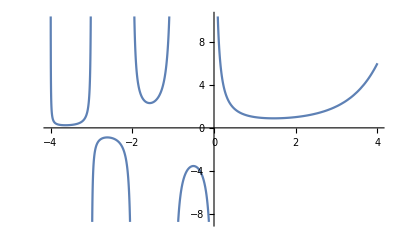

```mathematica
Plot[Gamma[x],{x,-4,4}]
```

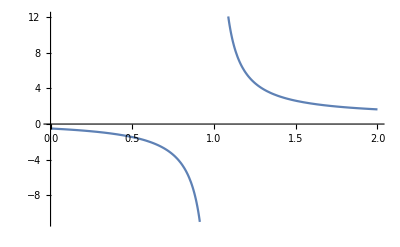

```mathematica
Plot[Zeta[x],{x,0,2}]
```

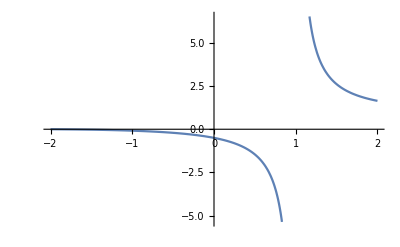

```mathematica
Plot[Zeta[x],{x,-2,2}]
```

```mathematica
Intergrate[Zeta[x],x]
```

Intergrate[Zeta[x],x]

```mathematica
Integrate[Zeta[x],x]
```

∫Zeta[x]ⅆx

```mathematica
Threshold[-Graphics-,{"Hard","Cluster"}]
```

-Graphics-

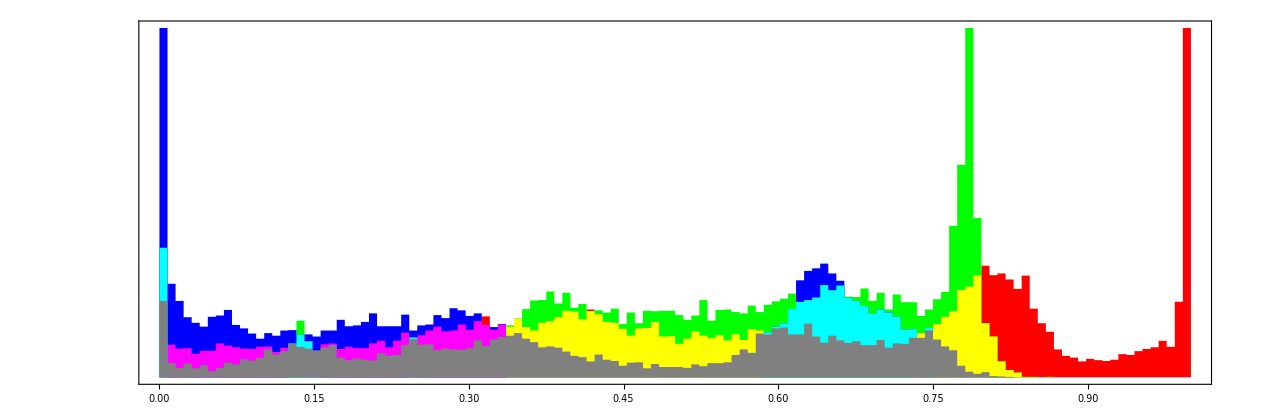

```mathematica
ImageHistogram[-Graphics-]
```

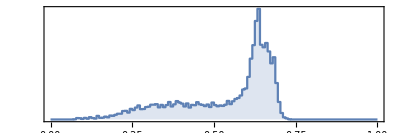

```mathematica
ImageHistogram[-Graphics-]
```

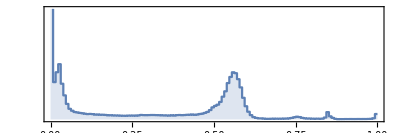

```mathematica
ImageHistogram[-Graphics3D-]
```

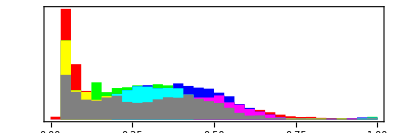

```mathematica
ImageHistogram[-Graphics-,32]
```

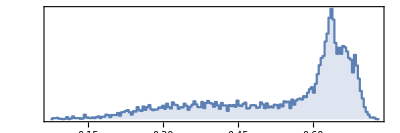

```mathematica
ImageHistogram[-Graphics-,All]
```

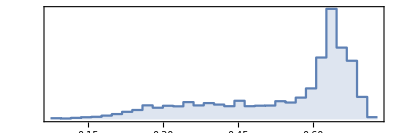

```mathematica
ImageHistogram[-Graphics-,32,All]
```

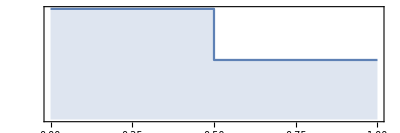

```mathematica
ImageHistogram[-Graphics-]
```

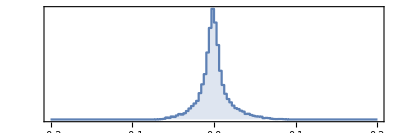

```mathematica
ImageHistogram[LaplacianGaussianFilter[-Graphics-,3],Automatic,{-.2,.2},FrameTicks->{True,False}]
```

```mathematica
Today[]
```

Day: Thu 6 Jun 2019[]

```mathematica
Day
```

```mathematica
Interpreter["DayOfWeek"]["Monday"]
```

Monday

```mathematica
DayOfWeek[{1776,7,4}]
```

DayOfWeek[{1776,7,4}]

```mathematica
Needs["Calendar`"]
```

DayOfWeek::shdw: Symbol DayOfWeek appears in multiple contexts {Calendar`,Global`}; definitions in context Calendar` may shadow or be shadowed by other definitions.

```mathematica
Global`
```

```mathematica
Names["Global`*"]
```

{a,Global`DayOfWeek,e,expr,i,Intergrate,opts,Rubi100,Rubi101,Rubi102,Rubi103,Rubi104,Rubi105,Rubi106,Rubi107,Rubi108,Rubi109,Rubi110,Rubi111,Rubi112,Rubi113,Rubi114,Rubi115,Rubi116,Rubi117,Rubi118,Rubi119,Rubi120,Rubi121,Rubi122,Rubi123,Rubi124,Rubi125,Rubi126,Rubi127,Rubi128,Rubi129,Rubi130,Rubi131,Rubi132,Rubi133,Rubi134,Rubi135,Rubi136,Rubi137,Rubi138,Rubi139,Rubi140,Rubi141,Rubi142,Rubi143,Rubi144,Rubi145,Rubi146,Rubi147,Rubi148,Rubi149,Rubi150,Rubi151,Rubi152,Rubi153,Rubi154,Rubi155,Rubi156,Rubi157,Rubi158,Rubi159,Rubi160,Rubi161,Rubi162,Rubi163,Rubi164,Rubi165,Rubi166,Rubi167,Rubi168,Rubi169,Rubi170,Rubi171,Rubi172,Rubi173,Rubi174,Rubi175,Rubi176,Rubi177,Rubi178,Rubi179,Rubi180,Rubi181,Rubi182,Rubi183,Rubi184,Rubi185,Rubi186,Rubi187,Rubi188,Rubi189,Rubi190,Rubi191,Rubi192,Rubi193,Rubi194,Rubi195,Rubi196,Rubi197,Rubi198,Rubi199,Rubi200,Rubi201,Rubi202,Rubi203,Rubi204,Rubi205,Rubi206,Rubi207,Rubi208,Rubi209,Rubi210,Rubi211,Rubi212,Rubi213,Rubi214,Rubi215,Rubi216,Rubi217,Rubi218,Rubi219,Rubi220,Rubi221,Rubi222,Rubi223,Rubi224,Rubi225,Rubi226,Rubi227,Rubi228,Rubi229,Rubi230,Rubi231,Rubi232,Rubi233,Rubi234,Rubi235,Rubi236,Rubi237,Rubi238,Rubi239,Rubi240,Rubi241,Rubi242,Rubi243,Rubi244,Rubi245,Rubi246,Rubi247,Rubi248,Rubi249,Rubi250,Rubi251,Rubi252,Rubi253,Rubi254,Rubi255,Rubi256,Rubi257,Rubi258,Rubi259,Rubi260,Rubi261,Rubi262,Rubi263,Rubi264,Rubi265,Rubi266,Rubi267,Rubi268,Rubi269,Rubi270,Rubi271,Rubi272,Rubi273,Rubi274,Rubi275,Rubi276,Rubi277,Rubi278,Rubi279,Rubi280,Rubi281,Rubi282,Rubi283,Rubi284,Rubi285,Rubi286,Rubi287,Rubi288,Rubi65,Rubi66,Rubi67,Rubi68,Rubi69,Rubi70,Rubi71,Rubi72,Rubi73,Rubi74,Rubi75,Rubi76,Rubi77,Rubi78,Rubi79,Rubi80,Rubi81,Rubi82,Rubi83,Rubi84,Rubi85,Rubi86,Rubi87,Rubi88,Rubi89,Rubi90,Rubi91,Rubi92,Rubi93,Rubi94,Rubi95,Rubi96,Rubi97,Rubi98,Rubi99,s,uspec,x,x$,$20,$21,$22,$23,$25,$26,$27,$28,$29,$30,$32,$33,$34,$35,$36,$37,$38,$39,$40,$41}

```mathematica
Global`DayOfWeek[Today[]]
```

Global`DayOfWeek[Day: Thu 6 Jun 2019[]]